```mathematica
Binomial
```

```mathematica
BinomialDistribution[n,p]
```

```mathematica
Manipulate[DiscretePlot[{PDF[BinomialDistribution[n,0.6/n],k],PDF[PoissonDistribution[0.6],k]},{k,1,n,1},PlotRange->All,PlotMarkers->Automatic,AxesOrigin->{0,0},PlotLabel->N==n],{n,1,100,1}]
```

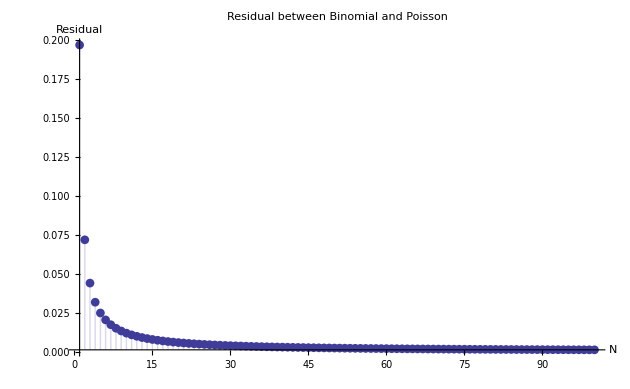

```mathematica
DiscretePlot[Max[Table[{Abs[(PDF[BinomialDistribution[n,0.5/n],k]-PDF[PoissonDistribution[0.5],k])
]},{k,1,n,1}
]
],
{n,1,100,1},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"N","Residual"},PlotLabel->"Residual between Binomial and Poisson"]
```

```mathematica
Manipulate[Plot[{CDF[PoissonDistribution[λ],Sqrt[λ]k+λ],CDF[NormalDistribution[0,1],k]},{k,-10,10},AxesOrigin->{0,0}],{λ,1,100,1}]
```

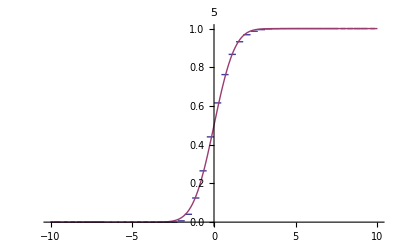
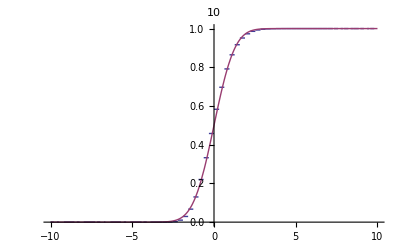
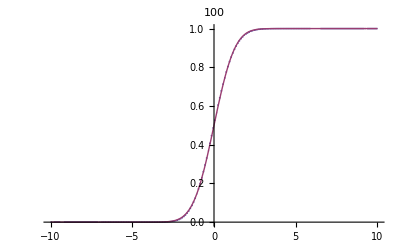

```mathematica
Table[Plot[{CDF[PoissonDistribution[λ],Sqrt[λ]k+λ],CDF[NormalDistribution[0,1],k]},{k,-10,10},AxesOrigin->{0,0},PlotLabel->λ],{λ,{5,10,100}}]
```